## 131Ba

```mathematica
ClearAll["Global`*"]
```

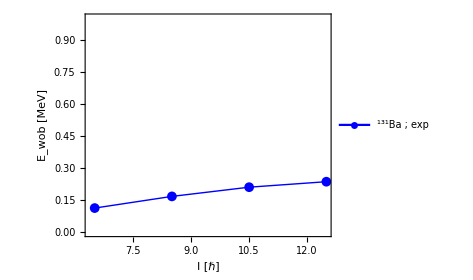

```mathematica
yrastEn=Sort[{3717.3,2611.14,1682.61,898.23,286.86}];
wob1En=Sort[{3400.7,2357.72,1458.24,705.86}];
yrastSpin=Table[i/2,{i,11,27,4}];
wob1Spin=Table[i/2,{i,13,25,4}];
wobbling[yrast_,b1_,spins_]:=Table[{spins[[i]],b1[[i]]/1000-1/2(yrast[[i]]+yrast[[i+1]])/1000},{i,1,Length[b1]}];
data=wobbling[yrastEn,wob1En,wob1Spin];
fig=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{18,Bold,Black},PlotLegends->Placed[{Row[{Superscript["","131"],"Ba ; exp"}]},{0.3,0.9}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/131Ba.pdf",fig];
Show[fig]
```